```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}]
```

{{bitonic_2n_float_sort_bench/8,1301590,501.561,502.419,ns,,,,,,8},{bitonic_2n_float_sort_bench/16,1298567,520.569,521.15,ns,,,,,,16},{bitonic_2n_float_sort_bench/32,1162285,589.733,591.858,ns,,,,,,32},{bitonic_2n_float_sort_bench/64,882510,785.21,786.34,ns,,,,,,64},{bitonic_2n_float_sort_bench/128,542217,1264.39,1265.58,ns,,,,,,128},{bitonic_2n_float_sort_bench/256,299001,2347.07,2350.62,ns,,,,,,256},{bitonic_2n_float_sort_bench/512,153455,4746.93,4748.83,ns,,,,,,512},{bitonic_2n_float_sort_bench/1024,65097,10359.4,10390.5,ns,,,,,,1024},{bitonic_2n_float_sort_bench/2048,30016,23082.6,23159.3,ns,,,,,,2048},{bitonic_2n_float_sort_bench/4096,13416,52434.4,52582.6,ns,,,,,,4096},{bitonic_2n_float_sort_bench/8192,5665,118200,118423,ns,,,,,,8192},{bitonic_2n_float_sort_bench/16384,2690,267566,267860,ns,,,,,,16384},{bitonic_2n_float_sort_bench/32768,1058,597817,598114,ns,,,,,,32768},{bitonic_2n_float_sort_bench/65536,525,1.2833×10^6,1.28342×10^6,ns,,,,,,65536},{bitonic_2n_float_sort_bench/131072,235,2.94281×10^6,2.93896×10^6,ns,,,,,,131072},{bitonic_2n_float_sort_bench/262144,96,6.6999×10^6,6.70012×10^6,ns,,,,,,262144},{bitonic_2n_float_sort_bench/524288,44,1.53632×10^7,1.53633×10^7,ns,,,,,,524288},{bitonic_2n_float_sort_bench/1048576,20,3.46816×10^7,3.46816×10^7,ns,,,,,,1.04858×10^6},{bitonic_2n_float_sort_bench/2097152,8,8.01656×10^7,8.01648×10^7,ns,,,,,,2.09715×10^6},{bitonic_2n_float_sort_bench/4194304,4,1.77558×10^8,1.77552×10^8,ns,,,,,,4.1943×10^6},{bitonic_2n_float_sort_bench/8388608,2,3.99575×10^8,3.99565×10^8,ns,,,,,,8.38861×10^6},{bitonic_2n_float_sort_bench/16777216,1,8.94934×10^8,8.94924×10^8,ns,,,,,,1.67772×10^7},{bitonic_2n_float_sort_bench/33554432,1,2.48659×10^9,2.48037×10^9,ns,,,,,,3.35544×10^7},{bitonic_2n_float_sort_bench/67108864,1,4.87838×10^9,4.84617×10^9,ns,,,,,,6.71089×10^7},{bitonic_2n_float_sort_bench_BigO,,71.6334,71.2387,N,,,,,,},{bitonic_2n_float_sort_bench_RMS,,0.224285,0.221579,,,,,,,},{bitonic_8n_float_sort_bench/8,1105812,590.466,590.7,ns,,,,,,8},{bitonic_8n_float_sort_bench/64,685267,980.481,982.888,ns,,,,,,64},{bitonic_8n_float_sort_bench/512,133589,5749.44,5741.03,ns,,,,,,512},{bitonic_8n_float_sort_bench/4096,9718,61631.3,61735.7,ns,,,,,,4096},{bitonic_8n_float_sort_bench/32768,905,628643,629067,ns,,,,,,32768},{bitonic_8n_float_sort_bench/262144,95,7.3512×10^6,7.35161×10^6,ns,,,,,,262144},{bitonic_8n_float_sort_bench/2097152,8,9.55958×10^7,9.55939×10^7,ns,,,,,,2.09715×10^6},{bitonic_8n_float_sort_bench/16777216,1,1.09216×10^9,1.09204×10^9,ns,,,,,,1.67772×10^7},{bitonic_8n_float_sort_bench/67108864,1,5.0787×10^9,5.07867×10^9,ns,,,,,,6.71089×10^7},{bitonic_8n_float_sort_bench_BigO,,75.0284,75.0276,N,,,,,,},{bitonic_8n_float_sort_bench_RMS,,0.087682,0.0877329,,,,,,,},{bitonic_float_sort_bench/8,1380681,528.961,529.852,ns,,,,,,8},{bitonic_float_sort_bench/16,1194481,544.398,544.668,ns,,,,,,16},{bitonic_float_sort_bench/32,1036150,657.772,659.329,ns,,,,,,32},{bitonic_float_sort_bench/64,833169,820.23,821.878,ns,,,,,,64},{bitonic_float_sort_bench/128,501820,1480.31,1474.13,ns,,,,,,128},{bitonic_float_sort_bench/256,315395,2165.51,2168.06,ns,,,,,,256},{bitonic_float_sort_bench/512,159635,4385.08,4386.94,ns,,,,,,512},{bitonic_float_sort_bench/1024,69275,9881.16,9901.58,ns,,,,,,1024},{bitonic_float_sort_bench/2048,31671,21826.4,21873.3,ns,,,,,,2048},{bitonic_float_sort_bench/4096,12863,49502.7,49591,ns,,,,,,4096},{bitonic_float_sort_bench/8192,5846,113070,113211,ns,,,,,,8192},{bitonic_float_sort_bench/16384,2807,243446,243640,ns,,,,,,16384},{bitonic_float_sort_bench/32768,1192,632503,632856,ns,,,,,,32768},{bitonic_float_sort_bench/65536,429,1.36688×10^6,1.36678×10^6,ns,,,,,,65536},{bitonic_float_sort_bench/131072,248,2.82692×10^6,2.82723×10^6,ns,,,,,,131072},{bitonic_float_sort_bench/262144,99,6.42416×10^6,6.42446×10^6,ns,,,,,,262144},{bitonic_float_sort_bench/524288,46,1.46952×10^7,1.46942×10^7,ns,,,,,,524288},{bitonic_float_sort_bench/1048576,15,4.08905×10^7,4.08902×10^7,ns,,,,,,1.04858×10^6},{bitonic_float_sort_bench/2097152,6,9.44746×10^7,9.44749×10^7,ns,,,,,,2.09715×10^6},{bitonic_float_sort_bench/4194304,3,2.18943×10^8,2.18944×10^8,ns,,,,,,4.1943×10^6},{bitonic_float_sort_bench/8388608,1,5.09388×10^8,5.09121×10^8,ns,,,,,,8.38861×10^6},{bitonic_float_sort_bench/16777216,1,1.09553×10^9,1.09552×10^9,ns,,,,,,1.67772×10^7},{bitonic_float_sort_bench/33554432,1,2.342×10^9,2.34178×10^9,ns,,,,,,3.35544×10^7},{bitonic_float_sort_bench/67108864,1,4.41557×10^9,4.41555×10^9,ns,,,,,,6.71089×10^7},{bitonic_float_sort_bench_BigO,,66.4019,66.4001,N,,,,,,},{bitonic_float_sort_bench_RMS,,0.0871446,0.0871077,,,,,,,},{std_float_sort_bench/8,1122669,586.475,588.547,ns,,,,,,8},{std_float_sort_bench/16,942504,715.769,719.032,ns,,,,,,16},{std_float_sort_bench/32,508461,1344.83,1354.38,ns,,,,,,32},{std_float_sort_bench/64,277268,2518.48,2535.67,ns,,,,,,64},{std_float_sort_bench/128,127942,5122.89,5151.58,ns,,,,,,128},{std_float_sort_bench/256,63565,10986.2,11049.4,ns,,,,,,256},{std_float_sort_bench/512,29211,23838.3,23948.7,ns,,,,,,512},{std_float_sort_bench/1024,13033,52317.7,52513.7,ns,,,,,,1024},{std_float_sort_bench/2048,6068,113843,114197,ns,,,,,,2048},{std_float_sort_bench/4096,2817,247756,248321,ns,,,,,,4096},{std_float_sort_bench/8192,1301,536203,536954,ns,,,,,,8192},{std_float_sort_bench/16384,597,1.14982×10^6,1.15066×10^6,ns,,,,,,16384},{std_float_sort_bench/32768,285,2.42721×10^6,2.42794×10^6,ns,,,,,,32768},{std_float_sort_bench/65536,133,5.16349×10^6,5.16408×10^6,ns,,,,,,65536},{std_float_sort_bench/131072,61,1.09551×10^7,1.09559×10^7,ns,,,,,,131072},{std_float_sort_bench/262144,30,2.30597×10^7,2.30602×10^7,ns,,,,,,262144},{std_float_sort_bench/524288,14,4.91849×10^7,4.91855×10^7,ns,,,,,,524288},{std_float_sort_bench/1048576,7,1.02123×10^8,1.02123×10^8,ns,,,,,,1.04858×10^6},{std_float_sort_bench/2097152,3,2.14601×10^8,2.14598×10^8,ns,,,,,,2.09715×10^6},{std_float_sort_bench/4194304,2,4.48082×10^8,4.48082×10^8,ns,,,,,,4.1943×10^6},{std_float_sort_bench/8388608,1,9.37155×10^8,9.37146×10^8,ns,,,,,,8.38861×10^6},{std_float_sort_bench/16777216,1,1.96666×10^9,1.96664×10^9,ns,,,,,,1.67772×10^7},{std_float_sort_bench/33554432,1,4.11756×10^9,4.11754×10^9,ns,,,,,,3.35544×10^7},{std_float_sort_bench/67108864,1,8.43663×10^9,8.43661×10^9,ns,,,,,,6.71089×10^7},{std_float_sort_bench_BigO,,124.511,124.51,N,,,,,,},{std_float_sort_bench_RMS,,0.0640562,0.0640594,,,,,,,}}

```mathematica
benchmarks={"bitonic_2n_float_sort_bench", "bitonic_8n_float_sort_bench","bitonic_float_sort_bench", "std_float_sort_bench"};
cols
```

{name,iterations,real_time,cpu_time,time_unit,bytes_per_second,items_per_second,label,error_occurred,error_message,Number to sort:}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringPosition[data[[i,1]], name]//Length  && Length[data[[i]]]>5)≠0,data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]];
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=Transpose[{NumToSort3,timing3}];
p4=Transpose[{NumToSort4,timing4}];
```

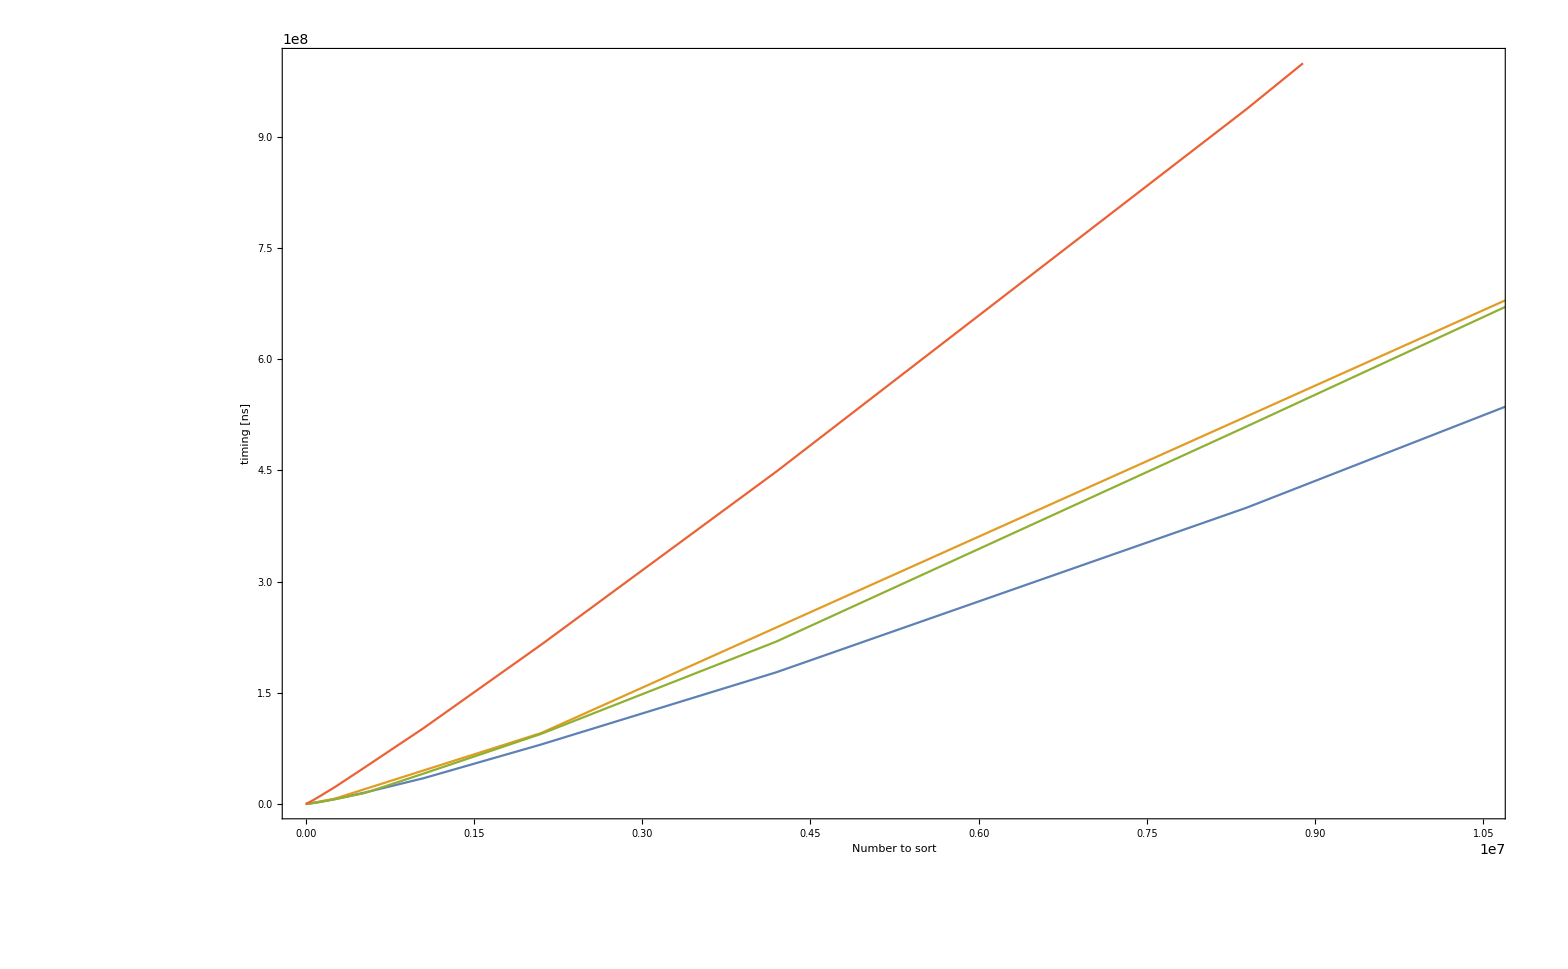

```mathematica
ListLinePlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]}]
```

```mathematica
NonlinearModelFit[p1,a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[p2,a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[p3,a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[p4,a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[-174.891 x-6.31851×10^-7 x^2+0.891862 x Log[x]^2]

FittedModel[-22.539 x-9.75548×10^-8 x^2+0.322562 x Log[x]^2]

FittedModel[-51.9844 x-4.43224×10^-7 x^2+0.454273 x Log[x]^2]

FittedModel[37.1681 x-1.24112×10^-7 x^2+0.298307 x Log[x]^2]